```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/HiggsR2GW/math

```mathematica
coord=Join[Table[Subscript[x, i][t],{i,4}],{y[t]}]
mom=D[coord, t]
n=Length[coord]
```

{x_1[t],x_2[t],x_3[t],x_4[t],y[t]}

{x_1'[t],x_2'[t],x_3'[t],x_4'[t],y'[t]}

5

```mathematica
λ=10^-2;
ξg=4089;(*Sqrt[2 10^9 λ]/.{λ->10^-2}*)
ξΓ=0;
α=((3 10^4)^2)/3;(*ξg^2/.{ξg->Sqrt[2 10^9 λ]/.{λ->10^-2}}*)
```

```mathematica
metric=Table[If[i<=4&&j<=4,Exp[-Sqrt[2/3]coord[[5]]](KroneckerDelta[i,j]-(6 ξΓ^2 coord[[i]]coord[[j]])/(1+ξΓ Sum[coord[[k]]^2,{k,4}])),KroneckerDelta[i,j]],{i,n},{j,n}];metric//MatrixForm
```

(ⅇ^(-√(2/3) y[t]) | 0 | 0 | 0 | 0
0 | ⅇ^(-√(2/3) y[t]) | 0 | 0 | 0
0 | 0 | ⅇ^(-√(2/3) y[t]) | 0 | 0
0 | 0 | 0 | ⅇ^(-√(2/3) y[t]) | 0
0 | 0 | 0 | 0 | 1)

```mathematica
Table[D[Flatten[metric][[i]], coord[[j]]],{i,n^2},{j,n}]/.{y[t]->5}//N
```

{{0.,0.,0.,0.,-0.0137707},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,-0.0137707},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,-0.0137707},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,-0.0137707},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.}}

```mathematica
inversemetric=Simplify[Inverse[metric]];inversemetric//MatrixForm
```

(ⅇ^(√(2/3) y[t]) | 0 | 0 | 0 | 0
0 | ⅇ^(√(2/3) y[t]) | 0 | 0 | 0
0 | 0 | ⅇ^(√(2/3) y[t]) | 0 | 0
0 | 0 | 0 | ⅇ^(√(2/3) y[t]) | 0
0 | 0 | 0 | 0 | 1)

```mathematica
Table[D[Flatten[inversemetric][[i]], coord[[j]]],{i,n^2},{j,n}]/.{y[t]->5}//N
```

{{0.,0.,0.,0.,48.4121},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,48.4121},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,48.4121},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,48.4121},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.}}

```mathematica
viel=Transpose[Eigenvectors[inversemetric]].DiagonalMatrix[Sqrt[Eigenvalues[inversemetric]]].Inverse[Transpose[Eigenvectors[inversemetric]]]//Simplify;
```

```mathematica
viel.Transpose[viel]-inversemetric//Simplify
```

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
affine:=affine=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*(D[metric[[s,j]],coord[[k]]]+D[metric[[s,k]],coord[[j]]]-D[metric[[j,k]],coord[[s]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}]]
```

```mathematica
listaffine:=Table[If[UnsameQ[affine[[i,j,k]],0],{ToString[Γ[i,j,k]],affine[[i,j,k]]/.{y[t]->5}//N}],{i,1,n},{j,1,n},{k,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listaffine],Null],2],TableSpacing->{2,2}]
```

Γ[1, 5, 1] | -0.408248
Γ[2, 5, 2] | -0.408248
Γ[3, 5, 3] | -0.408248
Γ[4, 5, 4] | -0.408248
Γ[5, 1, 1] | 0.00688533
Γ[5, 2, 2] | 0.00688533
Γ[5, 3, 3] | 0.00688533
Γ[5, 4, 4] | 0.00688533

```mathematica
riemann:=riemann=Simplify[Table[D[affine[[i,j,l]],coord[[k]]]-D[affine[[i,j,k]],coord[[l]]]+Sum[affine[[s,j,l]]affine[[i,k,s]]-affine[[s,j,k]]affine[[i,l,s]],{s,1,n}],{i,1,n},{j,1,n},{k,1,n},{l,1,n}]]
```

```mathematica
listriemann:=Table[If[UnsameQ[riemann[[i,j,k,l]],0],{ToString[R[i,j,k,l]],riemann[[i,j,k,l]]/.{y[t]->5}//N}],{i,1,n},{j,1,n},{k,1,n},{l,1,k-1}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listriemann],Null],2],TableSpacing->{2,2}]
```

R[1, 2, 2, 1] | 0.00281092
R[1, 3, 3, 1] | 0.00281092
R[1, 4, 4, 1] | 0.00281092
R[1, 5, 5, 1] | 0.166667
R[2, 1, 2, 1] | -0.00281092
R[2, 3, 3, 2] | 0.00281092
R[2, 4, 4, 2] | 0.00281092
R[2, 5, 5, 2] | 0.166667
R[3, 1, 3, 1] | -0.00281092
R[3, 2, 3, 2] | -0.00281092
R[3, 4, 4, 3] | 0.00281092
R[3, 5, 5, 3] | 0.166667
R[4, 1, 4, 1] | -0.00281092
R[4, 2, 4, 2] | -0.00281092
R[4, 3, 4, 3] | -0.00281092
R[4, 5, 5, 4] | 0.166667
R[5, 1, 5, 1] | -0.00281092
R[5, 2, 5, 2] | -0.00281092
R[5, 3, 5, 3] | -0.00281092
R[5, 4, 5, 4] | -0.00281092

```mathematica
potU=λ/4 Exp[-2Sqrt[2/3]y[t]] Sum[coord[[i]]^2,{i,4}]^2+1/(4α)(1-Exp[-Sqrt[2/3]y[t]](1+(ξg+ξΓ)Sum[coord[[i]]^2,{i,4}]))^2//Simplify
```

1/400 ⅇ^(-2 √(2/3) y[t]) (x_1[t]^2+x_2[t]^2+x_3[t]^2+x_4[t]^2)^2+((-1+ⅇ^(-√(2/3) y[t]) (1+4089 (x_1[t]^2+x_2[t]^2+x_3[t]^2+x_4[t]^2)))^2)/1200000000

```mathematica
potU/.{Subscript[x, 1][t]->1,Subscript[x, 2][t]->2,Subscript[x, 3][t]->3,Subscript[x, 4][t]->4,y[t]->5}//N
```

0.00420356

```mathematica
Uprime=Table[D[potU, coord[[i]]],{i,n}]//Simplify;
Upp=inversemetric.Table[D[Uprime[[j]], coord[[i]]]-Sum[affine[[k,i,j]]Uprime[[k]],{k,n}],{i,n},{j,n}]//Simplify;
```

```mathematica
Uprime/.{Subscript[x, 1][t]->1,Subscript[x, 2][t]->2,Subscript[x, 3][t]->3,Subscript[x, 4][t]->4,y[t]->5}//N
Upp/.{Subscript[x, 1][t]->1,Subscript[x, 2][t]->2,Subscript[x, 3][t]->3,Subscript[x, 4][t]->4,y[t]->5}//N//MatrixForm
```

{0.0005607,0.0011214,0.0016821,0.0022428,-0.00686719}

(0.0382661 | 0.00443449 | 0.00665174 | 0.00886899 | -0.0407281
0.00443449 | 0.0449178 | 0.0133035 | 0.017738 | -0.0814563
0.00665174 | 0.0133035 | 0.0560041 | 0.026607 | -0.122184
0.00886899 | 0.017738 | 0.026607 | 0.0715248 | -0.162913
-0.000686902 | -0.0013738 | -0.00206071 | -0.00274761 | 0.0112164)

```mathematica
const={Subscript[x, 2][t]->0,Subscript[x, 3][t]->0,Subscript[x, 4][t]->0,Subscript[x, 2]'[t]->0,Subscript[x, 3]'[t]->0,Subscript[x, 4]'[t]->0};
```

```mathematica
Kin=1/2 mom.metric.mom/.const//Simplify;
Hubble=Sqrt[(Kin+potU)/3]/.const//Simplify;
eH=Kin/Hubble^2//Simplify;
```

```mathematica
Dmom=Table[D[mom[[i]], t]+Sum[affine[[i,j,k]]mom[[j]]mom[[k]],{j,n},{k,n}],{i,n}]/.const//Simplify;
```

```mathematica
bgEoM=Table[Simplify[Dmom[[i]]+3Hubble mom[[i]]+Sum[inversemetric[[i,j]]Uprime[[j]],{j,n}]]==0,{i,1,n,4}]/.const;
```

```mathematica
bgIC={7/100(*1*)(*1/Sqrt[ξg]*),0,0,0,4(*10*)};
```

```mathematica
Hi=Hubble/.Table[coord[[i]]->bgIC[[i]],{i,n}]/.Table[mom[[i]]->0,{i,1,n,4}];Hi//N
```

6.32024×10^-6

```mathematica
potU/.{Subscript[x, 1][t]->8/100,y[t]->4}/.const//N
```

1.50235×10^-10

```mathematica
Plot3D[10^9 potU/.{Subscript[x, 1][t]->x,y[t]->z}/.const,{x,-1/10,1/10},{z,-1,5},PlotRange->{0,1},WorkingPrecision->30(*,AxesLabel->{"ϕ/M_Pl","σ/M_Pl ","10^9V/M_Pl^4 "}*),ImageSize->Large,ViewPoint->{0,2,1.5}]
```

-Graphics3D-

```mathematica
tf=50 Hi^-1;
tf//N
```

7.91109×10^6

```mathematica
bgsol=NDSolve[Join[bgEoM,Table[coord[[i]]==bgIC[[i]]/.{t->0},{i,1,n,4}],Table[mom[[i]]==0/.{t->0},{i,1,n,4}],
{NN'[t]==Hubble,NN[0]==0}],{Subscript[x, 1][t],y[t],Subscript[x, 1]'[t],y'[t],Subscript[x, 1]''[t],y''[t],NN[t]},
{t,0,tf},WorkingPrecision->30,MaxSteps->10^6][[1]];//AbsoluteTiming
```

{43.4515,Null}

```mathematica
x1sol[t_]=Subscript[x, 1][t]/.bgsol;
ysol[t_]=y[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
Hsol[t_]=Hubble/.bgsol;
eHsol[t_]=eH/.bgsol;
```

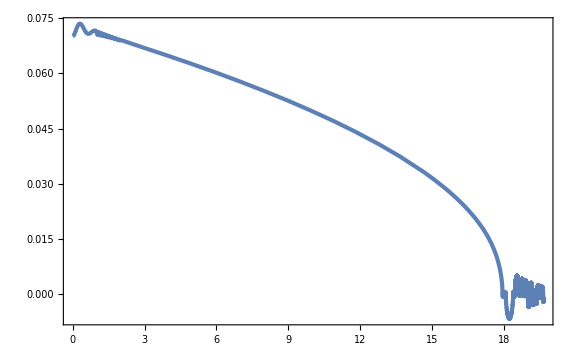

```mathematica
ParametricPlot[{Nsol[t],x1sol[t]},{t,0,tf},PlotRange->Full]
```

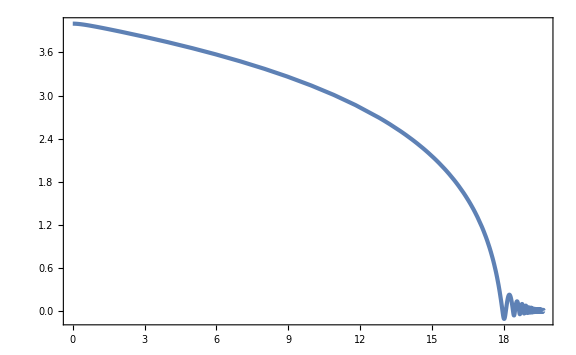

```mathematica
ParametricPlot[{Nsol[t],ysol[t]},{t,0,tf},PlotRange->Full]
```

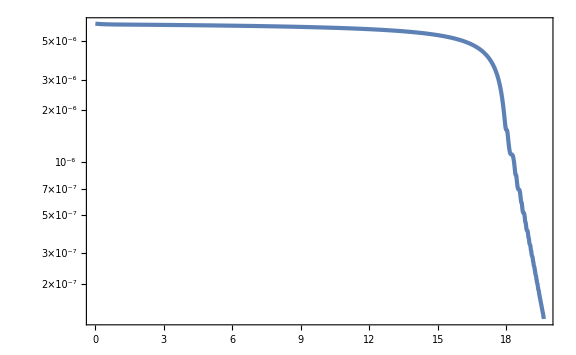

```mathematica
ParametricPlot[{Nsol[t],Hsol[t]},{t,0,tf},ScalingFunctions->{"Linear","Log"},PlotRange->Full]
```

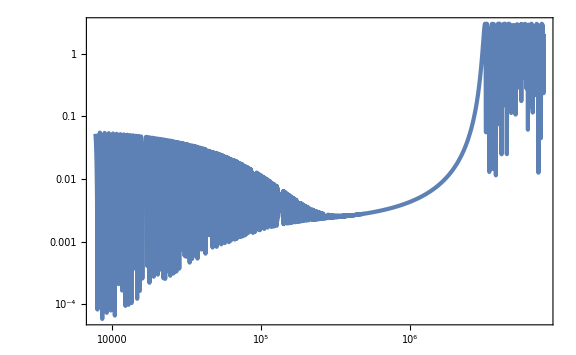

```mathematica
LogLogPlot[eHsol[t],{t,0,tf}]
```

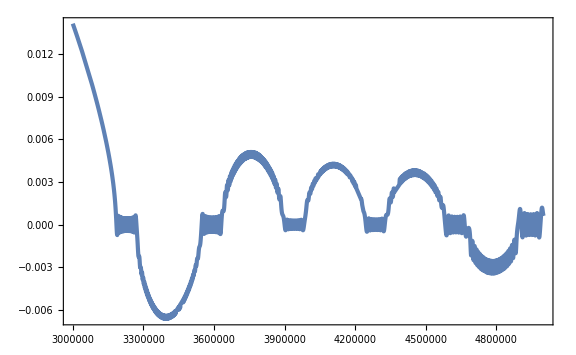

```mathematica
Plot[x1sol[t],{t,3 10^6,5 10^6},PlotRange->Full]
```

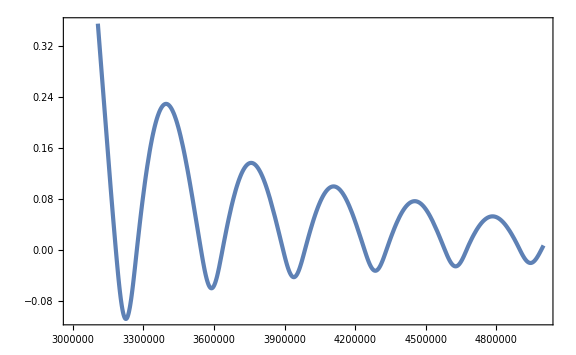

```mathematica
Plot[ysol[t],{t,3 10^6,5 10^6}]
```

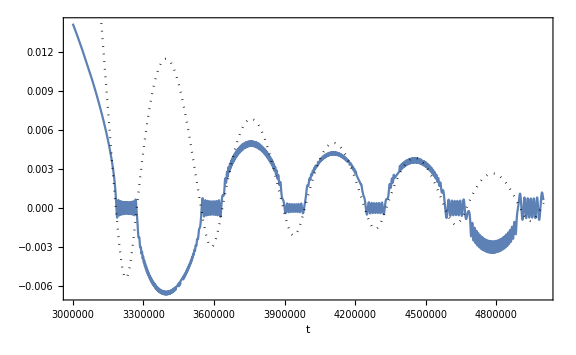

```mathematica
Plot[{x1sol[t],ysol[t]/20},{t,3 10^6,5 10^6},PlotStyle->{Automatic,{Black,Dotted}},FrameLabel->{t,None},WorkingPrecision->30]
```

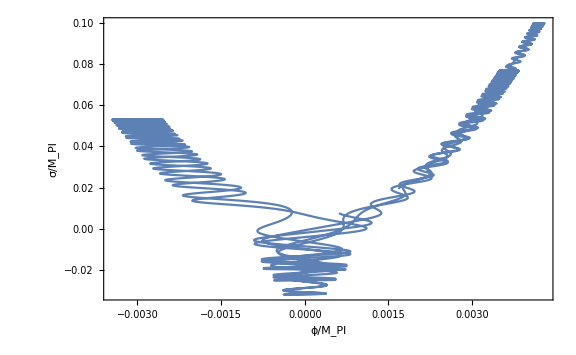

```mathematica
ParametricPlot[{x1sol[t],ysol[t]},{t,4 10^6,5 10^6},PlotStyle->Automatic,FrameLabel->{"ϕ/M_Pl","σ/M_Pl"}]
```

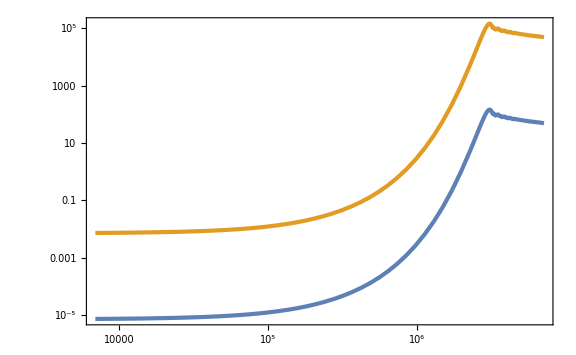

```mathematica
LogLogPlot[{E^Nsol[t] Hsol[t],1000 E^Nsol[t] Hsol[t]},{t,0,tf}]
```

```mathematica
dcoord=Table[Subscript[dx, i,a][t],{i,n},{a,n}]
dmom=D[dcoord, t];
Ddcoord=D[dcoord, t]+Table[Sum[affine[[i,j,k]]mom[[j]]dcoord[[k,a]],{j,n},{k,n}],{i,n},{a,n}]/.const//Simplify;
DDdcoord=D[Ddcoord, t]+Table[Sum[affine[[i,j,k]]mom[[j]]Ddcoord[[k,a]],{j,n},{k,n}],{i,n},{a,n}]/.const//Simplify;
```

{{dx_(1,1)[t],dx_(1,2)[t],dx_(1,3)[t],dx_(1,4)[t],dx_(1,5)[t]},{dx_(2,1)[t],dx_(2,2)[t],dx_(2,3)[t],dx_(2,4)[t],dx_(2,5)[t]},{dx_(3,1)[t],dx_(3,2)[t],dx_(3,3)[t],dx_(3,4)[t],dx_(3,5)[t]},{dx_(4,1)[t],dx_(4,2)[t],dx_(4,3)[t],dx_(4,4)[t],dx_(4,5)[t]},{dx_(5,1)[t],dx_(5,2)[t],dx_(5,3)[t],dx_(5,4)[t],dx_(5,5)[t]}}

```mathematica
Dmetric=Table[(3-eH)mom[[i]]mom[[j]]+1/Hubble(Dmom[[i]]mom[[j]]+mom[[i]]Dmom[[j]]),{i,n},{j,n}].metric/.const//Simplify;
```

```mathematica
qq=0.1;
ptbEoM=Flatten[ParallelTable[Simplify[DDdcoord[[i,a]]+3Hubble Ddcoord[[i,a]]-Sum[riemann[[i,j,k,l]]mom[[j]]mom[[k]]dcoord[[l,a]],{j,n},{k,n},{l,n}]+qq^2/E^(2NN[t])dcoord[[i,a]]+Sum[Upp[[i,j]]dcoord[[j,a]],{j,n}]/.const]==Simplify[(Dmetric.dcoord)[[i,a]]]/.bgsol,{i,n},{a,n}]];//AbsoluteTiming
```

{15.9482,Null}

```mathematica
ti=t/.FindRoot[1000 E^Nsol[t] Hsol[t]==qq,{t,10^6}]
```

438337.

```mathematica
ptbsol=NDSolve[Join[ptbEoM,Flatten[Table[dcoord[[i,a]]==1/(E^NN[t] Sqrt[2qq])viel[[i,a]] E^(I qq/E^NN[t] t)/.bgsol/.{t->ti},{i,n},{a,n}]],Flatten[Table[dmom[[i,a]]==D[1/(E^NN[t] Sqrt[2qq]), t]viel[[i,a]] E^(I qq/E^NN[t] t)/.{NN'[t]->Hsol[t]}/.bgsol/.{t->ti},{i,n},{a,n}]]],Flatten[dcoord],{t,ti,tf}][[1]];//AbsoluteTiming
```

{101.442,Null}

```mathematica
dcoordsol[t_]=dcoord/.ptbsol;
calP1[t_]=qq^3/(2 π^2)Sum[Abs[dcoordsol[t][[1,a]]]^2,{a,n}];
calPy[t_]=qq^3/(2 π^2)Sum[Abs[dcoordsol[t][[5,a]]]^2,{a,n}];
```

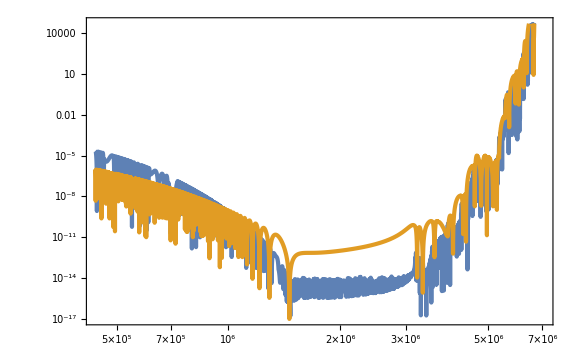

```mathematica
LogLogPlot[{calP1[t],calPy[t]},{t,ti,tf}]
```